# Discrete-time Quantum Walks (PoC)

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_],dim_]:=Chop[#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#]]&[env["Unitary"][dim+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_]]:=Chop[#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#]]&[env["Unitary"][Length[rho]/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_],dim_]:=With[{state=(#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#])&[env["Unitary"][dim+1]]},
Inner[Chop[#1*#2[dim+1].state.ConjugateTranspose[#2[dim+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
DTQWStep[rho_,DTQWEnv[env_]]:=With[{state=(#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#])&[env["Unitary"][Length[rho]/2+1]]},
Inner[Chop[#1*#2[Length[rho]/2+1].state.ConjugateTranspose[#2[Length[rho]/2+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,t],{t,n}];
ρ
]
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,t],{t,n}]
]
```

## Misc. functions

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

## Examples

## Operadores

```mathematica
α=π/6.;
```

```mathematica
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
```

```mathematica
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
```

```mathematica
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
```

```mathematica
FuzzyOperator[n_]:=RotateRight[IdentityMatrix[2*n,SparseArray],2]
```

```mathematica
FuzzyOperator[4]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

## Examples

### Classic random walk

```mathematica
probs=N[Binomial[#,Range[0,#]]/2^#]&/@Range[0,100];
expvals=DTQWPosExpvalue/@probs;
sds=DTQWPosStandardev/@probs;
```

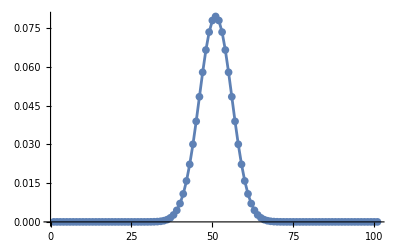

```mathematica
ListLinePlot[probs[[-1]],
PlotRange->All,
Mesh->All
]
```

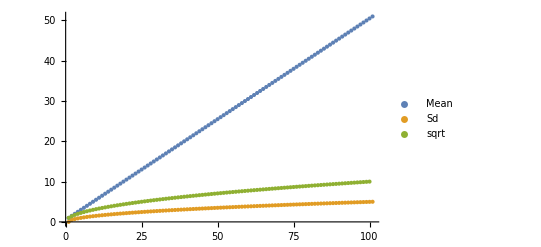

```mathematica
ListPlot[{expvals,sds,Sqrt[Range[100]]},
PlotLegends->{"Mean","Sd","sqrt"},
PlotRange->All
]
```

### Unitary DTQW

```mathematica
envC=DTQWEnv[<|"Type"->"ForwardGrowing","Decoherent"->False,"Unitary"->UnitaryOperator|>]
```

DTQWEnv[…]

```mathematica
coinC={1,ⅈ}/Sqrt[2.];
AbsoluteTiming[stepsC=DTQWTrace[coinC,100,envC];]
```

{1.47307,Null}

```mathematica
probsC=DTQWPosDistribution/@stepsC;
expvalsC=DTQWPosExpvalue/@probsC;
sdsC=DTQWPosStandardev/@probsC;
```

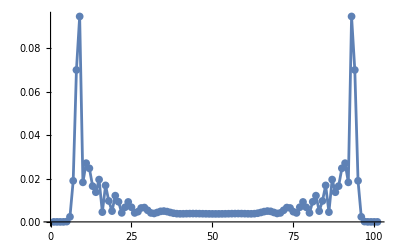

```mathematica
ListLinePlot[probsC[[-1]],
PlotRange->All,
Mesh->All
]
```

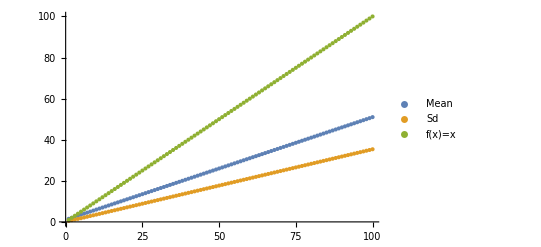

```mathematica
ListPlot[{expvalsC,sdsC,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

### DTQW w/fuzzy

#### 0.01 Decoherence

```mathematica
envO1=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.99,0.01},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO1={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO1=DTQWTrace[coinO1,100,envO1];]
```

{3.44659,Null}

```mathematica
probsO1=DTQWPosDistribution/@stepsO1;
expvalsO1=DTQWPosExpvalue/@probsO1;
sdsO1=DTQWPosStandardev/@probsO1;
```

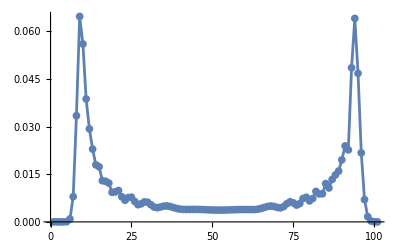

```mathematica
ListLinePlot[probsO1[[-1]],
PlotRange->All,
Mesh->All
]
```

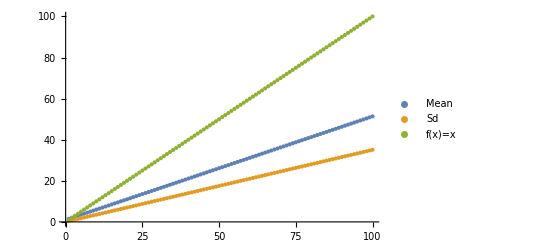

```mathematica
ListPlot[{expvalsO1,sdsO1,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 0.1 Decoherence

```mathematica
envO2=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.9,0.1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO2={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO2=DTQWTrace[coinO2,100,envO2];]
```

{3.55842,Null}

```mathematica
probsO2=DTQWPosDistribution/@stepsO2;
expvalsO2=DTQWPosExpvalue/@probsO2;
sdsO2=DTQWPosStandardev/@probsO2;
```

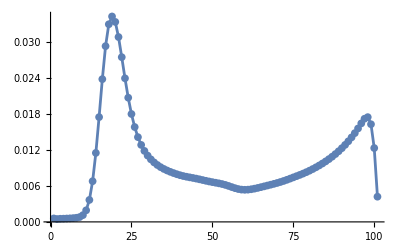

```mathematica
ListLinePlot[probsO2[[-1]],
PlotRange->All,
Mesh->All
]
```

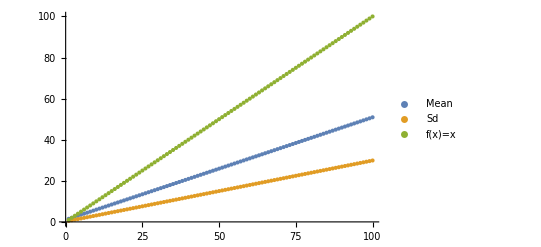

```mathematica
ListPlot[{expvalsO2,sdsO2,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 0.5 Decoherence

```mathematica
envO3=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO3={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO3=DTQWTrace[coinO3,100,envO3];]
```

{4.40889,Null}

```mathematica
probsO3=DTQWPosDistribution/@stepsO3;
expvalsO3=DTQWPosExpvalue/@probsO3;
sdsO3=DTQWPosStandardev/@probsO3;
```

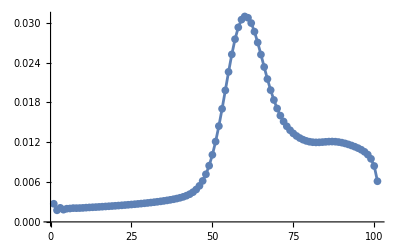

```mathematica
ListLinePlot[probsO3[[-1]],
PlotRange->All,
Mesh->All
]
```

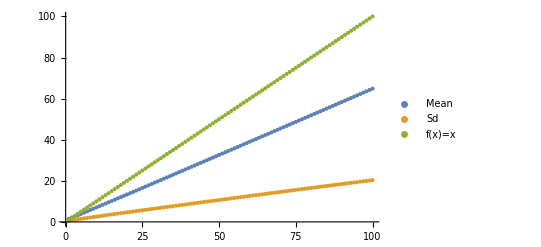

```mathematica
ListPlot[{expvalsO3,sdsO3,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 1 Decoherence

```mathematica
envO4=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0,1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO4={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO4=DTQWTrace[coinO4,100,envO4];]
```

{2.05938,Null}

```mathematica
probsO4=DTQWPosDistribution/@stepsO4;
expvalsO4=DTQWPosExpvalue/@probsO4;
sdsO4=DTQWPosStandardev/@probsO4;
```

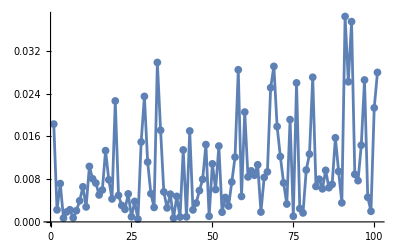

```mathematica
ListLinePlot[probsO4[[-1]],
PlotRange->All,
Mesh->All
]
```

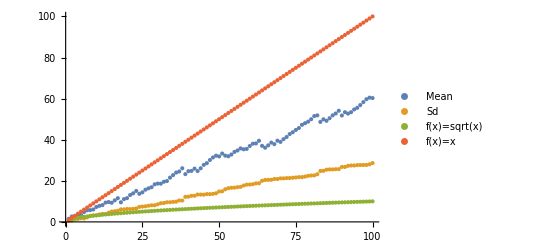

```mathematica
ListPlot[{expvalsO4,sdsO4,Sqrt[Range[100]],Range[100]},
PlotLegends->{"Mean","Sd","f(x)=sqrt(x)","f(x)=x"},
PlotRange->All
]
```

```mathematica
Manipulate[ListLinePlot[{probsC[[n]],probsO1[[n]],probsO2[[n]],probsO3[[n]]},
PlotRange->{{0,100},{0,0.13}},
PlotLegends->{"Cuántica","Decoherente 0.01","Decoherente 0.1","Decoherente 0.5"}
],{n,1,100,1}]
```

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification probsC⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO1⟦78⟧ is longer than depth of object.

Part::partd: Part specification probsO2⟦78⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.